```mathematica
distribution={};
For[xxx=1,xxx<3,xxx++,
Block[{distribution,xxx},Clear["Global`*"]];

profitfunction1[]:=(
q1=10-2*p1+p2;
profit1=p1*q1-c*q1-fix;

);

presentvalue1[]:=(
q1=10-2*p1+p2;
pv1=pv1+(q1*p1-q1*c-fix)*delta^(m-1);

);

profitfunction2[]:=(
q2=10-2*p2+p1;
profit2=q2*p2-q2*c-fix;


);


presentvalue2[]:=(
q2=10-2*p2+p1;
pv2=pv2+(q2*p2-q2*c-fix)*delta^(m-1);


);


model1[]:=(For[o=1,o<=11,o++,
(*Find a previously observed state*)
p1tmin1mod=RandomInteger[{1,10}];
p2tmin1mod=RandomInteger[{1,10}];
p1mod=RandomInteger[{1,10}];
p2mod=RandomInteger[{1,10}];
If[monnumber1[[(p1tmin1mod-1)*100+(p2tmin1mod-1)*10+p1mod]]>1  && monnumber2[[(p1tmin1mod-1)*100+(p2tmin1mod-1)*10+p2mod]]>1,
(*Did we observe these  state before?*)(*If so, we can find realistic profits in our matrix*)

profit1mod=monprofits1[[(p2mod-1)*10+p1mod]];




(*we are about to change to the new state*)(*we need to save up, so we can correct our believes*)
p1tmin1modst=p1tmin1mod;
p2tmin1modst=p2tmin1mod;
p1modst=p1mod;
profit1modst=profit1mod;


(*Change of state*)

p1tmin1mod=p1mod;
p2tmin1mod=p2mod;




(*AI's  turn for Company 1*)
(*Company 1 hasnt seen companies 2 decision*)



rand=RandomReal[];
maxspace={};
actionspace={};
Qvalues={};






For[i=1,i<Length[possibleprice]+1,i++,
Qvalues=montotals1[[(p1tmin1mod-1)*100+(p2tmin1mod-1)*10+possibleprice[[i]]]];
AppendTo[actionspace,Qvalues];
actionspace=Flatten[actionspace]]; 


max=Max[actionspace];


If[Length[Position[actionspace,max]]>1,For[i=1,i<Length[Position[actionspace,max]]+1,i++,t=Position[actionspace,max][[i]];
AppendTo[maxspace,t[[1]]]];
maxposi=maxspace[[RandomInteger[{1,Length[maxspace]}]]],maxposi=Flatten[Position[actionspace,max]][[1]]];



(*Company 1 now determined his quantity q1, but company 2 doesnt know anything about it*)(*we have to save up quantity 1 without letting company 2 know anything about it*)


(*Company 1 decides upon q1 based on the two options: Qvalues or average behaviour of agent2*)


z=RandomReal[];

numberspace={};
maxnumberspace={};
potentialsol={};
potentialspace={};



For[h=1,h<Length[possibleprice]+1,h++,
AppendTo[numberspace,monnumber2[[(p1tmin1mod-1)*100+(p2tmin1mod-1)*10+possibleprice[[h]]]]]];


Nk=Max[numberspace];
eta=Max[gama,et*1/(1+d*Sqrt[Nk])];
(*If z< eta, choose q1 based on Qvalues*)

If[z<eta,p1mod=possibleprice[[maxposi]]];

(*If z>=eta, choose q1 based on average behaviour of agent 2*)

If[z>=eta,
If[Length[Position[numberspace,Nk]]>1,For[i=1,i<Length[Position[numberspace,Nk]]+1,i++,t=Position[numberspace,Nk][[i]];
AppendTo[maxnumberspace,t[[1]]]];
numbposi=maxnumberspace[[RandomInteger[{1,Length[maxnumberspace]}]]],numbposi=Flatten[Position[numberspace,Nk]][[1]]]];

If[z>=eta,p2aver=possibleprice[[numbposi]]];
If[z>=eta,


For[i=1,i<Length[possibleprice]+1,i++,AppendTo[potentialsol,monprofits1[[(p2aver-1)*10+possibleprice[[i]]]]]];
maxfunction=Max[potentialsol];


If[Length[Position[potentialsol,maxfunction]]>1,For[i=1,i<Length[Position[potentialsol,maxfunction]]+1,i++,t=Position[potentialsol,maxfunction][[i]];
AppendTo[potentialspace,t[[1]]]];
maxpotential=potentialspace[[RandomInteger[{1,Length[potentialspace]}]]],maxpotential=Flatten[Position[potentialsol,maxfunction]][[1]]];

p1mod=possibleprice[[maxpotential]]];




(*time to adjust our believes (Q-values)*)
(*Q1-values*)

montotals1[[(p1tmin1modst-1)*100+(p2tmin1modst-1)*10+p1modst]]=montotals1[[(p1tmin1modst-1)*100+(p2tmin1modst-1)*10+p1modst]]+alpha*(profit1modst+delta*montotals1[[(p1tmin1mod-1)*100+(p2tmin1mod-1)*10+p1mod]]-montotals1[[(p1tmin1modst-1)*100+(p2tmin1modst-1)*10+p1modst]]);
]]);

model2[]:=(For[o=1,o<=11,o++,
(*Find a previously observed state*)
p1tmin1mod=RandomInteger[{1,10}];
p2tmin1mod=RandomInteger[{1,10}];
p1mod=RandomInteger[{1,10}];
p2mod=RandomInteger[{1,10}];
If[monnumber1[[(p1tmin1mod-1)*100+(p2tmin1mod-1)*10+p1mod]]>1  && monnumber2[[(p1tmin1mod-1)*100+(p2tmin1mod-1)*10+p2mod]]>1,
(*Did we observe these  state before?*)(*If so, we can find realistic profits in our matrix*)

profit2mod=monprofits2[[(p1mod-1)*10+p2mod]];




(*we are about to change to the new state*)(*we need to save up, so we can correct our believes*)
p1tmin1modst=p1tmin1mod;
p2tmin1modst=p2tmin1mod;
p2modst=p2mod;
profit2modst=profit2mod;


(*Change of state*)

p1tmin1mod=p1mod;
p2tmin1mod=p2mod;




(*AI's  turn for Company 1*)
(*Company 1 hasnt seen companies 2 decision*)



rand=RandomReal[];
maxspace={};
actionspace={};
Qvalues={};








For[i=1,i<Length[possibleprice]+1,i++,
Qvalues=montotals2[[(p1tmin1mod-1)*100+(p2tmin1mod-1)*10+possibleprice[[i]]]];
AppendTo[actionspace,Qvalues];
actionspace=Flatten[actionspace]]; 


max=Max[actionspace];

If[Length[Position[actionspace,max]]>1,For[i=1,i<Length[Position[actionspace,max]]+1,i++,t=Position[actionspace,max][[i]];
AppendTo[maxspace,t[[1]]]];
maxposi=maxspace[[RandomInteger[{1,Length[maxspace]}]]],maxposi=Flatten[Position[actionspace,max]][[1]]];




(*Company 2 decides upon q2 based on the two options: Qvalues or average behaviour of agent1*)


z=RandomReal[];

numberspace={};
maxnumberspace={};
potentialsol={};
potentialspace={};




For[h=1,h<Length[possibleprice]+1,h++,
AppendTo[numberspace,monnumber1[[(p1tmin1mod-1)*100+(p2tmin1mod-1)*10+possibleprice[[h]]]]]];

Nk=Max[numberspace];
eta=Max[gama,et*1/(1+d*Sqrt[Nk])];
(*If z< eta, choose q1 based on Qvalues*)

If[z<eta,p2mod=possibleprice[[maxposi]]];

(*If z>=eta, choose q1 based on average behaviour of agent 2*)

If[z>=eta,
If[Length[Position[numberspace,Nk]]>1,For[i=1,i<Length[Position[numberspace,Nk]]+1,i++,t=Position[numberspace,Nk][[i]];
AppendTo[maxnumberspace,t[[1]]]];
numbposi=maxnumberspace[[RandomInteger[{1,Length[maxnumberspace]}]]],numbposi=Flatten[Position[numberspace,Nk]][[1]]]];

If[z>=eta,p1aver=possibleprice[[numbposi]]];
If[z>=eta,

For[i=1,i<Length[possibleprice]+1,i++,AppendTo[potentialsol,monprofits2[[(p1aver-1)*10+possibleprice[[i]]]]]];
maxfunction=Max[potentialsol];


If[Length[Position[potentialsol,maxfunction]]>1,
For[i=1,i<Length[Position[potentialsol,maxfunction]]+1,i++,t=Position[potentialsol,maxfunction][[i]];
AppendTo[potentialspace,t[[1]]]];
maxpotential=potentialspace[[RandomInteger[{1,Length[potentialspace]}]]],maxpotential=Flatten[Position[potentialsol,maxfunction]][[1]]];

p2mod=possibleprice[[maxpotential]]];





(*time to adjust our believes (Q-values)*)
(*Q1-values*)

montotals2[[(p1tmin1modst-1)*100+(p2tmin1modst-1)*10+p2modst]]=montotals2[[(p1tmin1modst-1)*100+(p2tmin1modst-1)*10+p2modst]]+alpha*(profit2modst+delta*montotals2[[(p1tmin1mod-1)*100+(p2tmin1mod-1)*10+p2mod]]-montotals2[[(p1tmin1modst-1)*100+(p2tmin1modst-1)*10+p2modst]]);
]]
);

(*initialization*)



monQstate1={{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{1,1,10},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8},{1,2,9},{1,2,10},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,8},{1,3,9},{1,3,10},{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5},{1,4,6},{1,4,7},{1,4,8},{1,4,9},{1,4,10},{1,5,1},{1,5,2},{1,5,3},{1,5,4},{1,5,5},{1,5,6},{1,5,7},{1,5,8},{1,5,9},{1,5,10},{1,6,1},{1,6,2},{1,6,3},{1,6,4},{1,6,5},{1,6,6},{1,6,7},{1,6,8},{1,6,9},{1,6,10},{1,7,1},{1,7,2},{1,7,3},{1,7,4},{1,7,5},{1,7,6},{1,7,7},{1,7,8},{1,7,9},{1,7,10},{1,8,1},{1,8,2},{1,8,3},{1,8,4},{1,8,5},{1,8,6},{1,8,7},{1,8,8},{1,8,9},{1,8,10},{1,9,1},{1,9,2},{1,9,3},{1,9,4},{1,9,5},{1,9,6},{1,9,7},{1,9,8},{1,9,9},{1,9,10},{1,10,1},{1,10,2},{1,10,3},{1,10,4},{1,10,5},{1,10,6},{1,10,7},{1,10,8},{1,10,9},{1,10,10},{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,1,5},{2,1,6},{2,1,7},{2,1,8},{2,1,9},{2,1,10},{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,2,5},{2,2,6},{2,2,7},{2,2,8},{2,2,9},{2,2,10},{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,3,8},{2,3,9},{2,3,10},{2,4,1},{2,4,2},{2,4,3},{2,4,4},{2,4,5},{2,4,6},{2,4,7},{2,4,8},{2,4,9},{2,4,10},{2,5,1},{2,5,2},{2,5,3},{2,5,4},{2,5,5},{2,5,6},{2,5,7},{2,5,8},{2,5,9},{2,5,10},{2,6,1},{2,6,2},{2,6,3},{2,6,4},{2,6,5},{2,6,6},{2,6,7},{2,6,8},{2,6,9},{2,6,10},{2,7,1},{2,7,2},{2,7,3},{2,7,4},{2,7,5},{2,7,6},{2,7,7},{2,7,8},{2,7,9},{2,7,10},{2,8,1},{2,8,2},{2,8,3},{2,8,4},{2,8,5},{2,8,6},{2,8,7},{2,8,8},{2,8,9},{2,8,10},{2,9,1},{2,9,2},{2,9,3},{2,9,4},{2,9,5},{2,9,6},{2,9,7},{2,9,8},{2,9,9},{2,9,10},{2,10,1},{2,10,2},{2,10,3},{2,10,4},{2,10,5},{2,10,6},{2,10,7},{2,10,8},{2,10,9},{2,10,10},{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,1,5},{3,1,6},{3,1,7},{3,1,8},{3,1,9},{3,1,10},{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,2,5},{3,2,6},{3,2,7},{3,2,8},{3,2,9},{3,2,10},{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5},{3,3,6},{3,3,7},{3,3,8},{3,3,9},{3,3,10},{3,4,1},{3,4,2},{3,4,3},{3,4,4},{3,4,5},{3,4,6},{3,4,7},{3,4,8},{3,4,9},{3,4,10},{3,5,1},{3,5,2},{3,5,3},{3,5,4},{3,5,5},{3,5,6},{3,5,7},{3,5,8},{3,5,9},{3,5,10},{3,6,1},{3,6,2},{3,6,3},{3,6,4},{3,6,5},{3,6,6},{3,6,7},{3,6,8},{3,6,9},{3,6,10},{3,7,1},{3,7,2},{3,7,3},{3,7,4},{3,7,5},{3,7,6},{3,7,7},{3,7,8},{3,7,9},{3,7,10},{3,8,1},{3,8,2},{3,8,3},{3,8,4},{3,8,5},{3,8,6},{3,8,7},{3,8,8},{3,8,9},{3,8,10},{3,9,1},{3,9,2},{3,9,3},{3,9,4},{3,9,5},{3,9,6},{3,9,7},{3,9,8},{3,9,9},{3,9,10},{3,10,1},{3,10,2},{3,10,3},{3,10,4},{3,10,5},{3,10,6},{3,10,7},{3,10,8},{3,10,9},{3,10,10},{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,1,5},{4,1,6},{4,1,7},{4,1,8},{4,1,9},{4,1,10},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,2,5},{4,2,6},{4,2,7},{4,2,8},{4,2,9},{4,2,10},{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,3,5},{4,3,6},{4,3,7},{4,3,8},{4,3,9},{4,3,10},{4,4,1},{4,4,2},{4,4,3},{4,4,4},{4,4,5},{4,4,6},{4,4,7},{4,4,8},{4,4,9},{4,4,10},{4,5,1},{4,5,2},{4,5,3},{4,5,4},{4,5,5},{4,5,6},{4,5,7},{4,5,8},{4,5,9},{4,5,10},{4,6,1},{4,6,2},{4,6,3},{4,6,4},{4,6,5},{4,6,6},{4,6,7},{4,6,8},{4,6,9},{4,6,10},{4,7,1},{4,7,2},{4,7,3},{4,7,4},{4,7,5},{4,7,6},{4,7,7},{4,7,8},{4,7,9},{4,7,10},{4,8,1},{4,8,2},{4,8,3},{4,8,4},{4,8,5},{4,8,6},{4,8,7},{4,8,8},{4,8,9},{4,8,10},{4,9,1},{4,9,2},{4,9,3},{4,9,4},{4,9,5},{4,9,6},{4,9,7},{4,9,8},{4,9,9},{4,9,10},{4,10,1},{4,10,2},{4,10,3},{4,10,4},{4,10,5},{4,10,6},{4,10,7},{4,10,8},{4,10,9},{4,10,10},{5,1,1},{5,1,2},{5,1,3},{5,1,4},{5,1,5},{5,1,6},{5,1,7},{5,1,8},{5,1,9},{5,1,10},{5,2,1},{5,2,2},{5,2,3},{5,2,4},{5,2,5},{5,2,6},{5,2,7},{5,2,8},{5,2,9},{5,2,10},{5,3,1},{5,3,2},{5,3,3},{5,3,4},{5,3,5},{5,3,6},{5,3,7},{5,3,8},{5,3,9},{5,3,10},{5,4,1},{5,4,2},{5,4,3},{5,4,4},{5,4,5},{5,4,6},{5,4,7},{5,4,8},{5,4,9},{5,4,10},{5,5,1},{5,5,2},{5,5,3},{5,5,4},{5,5,5},{5,5,6},{5,5,7},{5,5,8},{5,5,9},{5,5,10},{5,6,1},{5,6,2},{5,6,3},{5,6,4},{5,6,5},{5,6,6},{5,6,7},{5,6,8},{5,6,9},{5,6,10},{5,7,1},{5,7,2},{5,7,3},{5,7,4},{5,7,5},{5,7,6},{5,7,7},{5,7,8},{5,7,9},{5,7,10},{5,8,1},{5,8,2},{5,8,3},{5,8,4},{5,8,5},{5,8,6},{5,8,7},{5,8,8},{5,8,9},{5,8,10},{5,9,1},{5,9,2},{5,9,3},{5,9,4},{5,9,5},{5,9,6},{5,9,7},{5,9,8},{5,9,9},{5,9,10},{5,10,1},{5,10,2},{5,10,3},{5,10,4},{5,10,5},{5,10,6},{5,10,7},{5,10,8},{5,10,9},{5,10,10},{6,1,1},{6,1,2},{6,1,3},{6,1,4},{6,1,5},{6,1,6},{6,1,7},{6,1,8},{6,1,9},{6,1,10},{6,2,1},{6,2,2},{6,2,3},{6,2,4},{6,2,5},{6,2,6},{6,2,7},{6,2,8},{6,2,9},{6,2,10},{6,3,1},{6,3,2},{6,3,3},{6,3,4},{6,3,5},{6,3,6},{6,3,7},{6,3,8},{6,3,9},{6,3,10},{6,4,1},{6,4,2},{6,4,3},{6,4,4},{6,4,5},{6,4,6},{6,4,7},{6,4,8},{6,4,9},{6,4,10},{6,5,1},{6,5,2},{6,5,3},{6,5,4},{6,5,5},{6,5,6},{6,5,7},{6,5,8},{6,5,9},{6,5,10},{6,6,1},{6,6,2},{6,6,3},{6,6,4},{6,6,5},{6,6,6},{6,6,7},{6,6,8},{6,6,9},{6,6,10},{6,7,1},{6,7,2},{6,7,3},{6,7,4},{6,7,5},{6,7,6},{6,7,7},{6,7,8},{6,7,9},{6,7,10},{6,8,1},{6,8,2},{6,8,3},{6,8,4},{6,8,5},{6,8,6},{6,8,7},{6,8,8},{6,8,9},{6,8,10},{6,9,1},{6,9,2},{6,9,3},{6,9,4},{6,9,5},{6,9,6},{6,9,7},{6,9,8},{6,9,9},{6,9,10},{6,10,1},{6,10,2},{6,10,3},{6,10,4},{6,10,5},{6,10,6},{6,10,7},{6,10,8},{6,10,9},{6,10,10},{7,1,1},{7,1,2},{7,1,3},{7,1,4},{7,1,5},{7,1,6},{7,1,7},{7,1,8},{7,1,9},{7,1,10},{7,2,1},{7,2,2},{7,2,3},{7,2,4},{7,2,5},{7,2,6},{7,2,7},{7,2,8},{7,2,9},{7,2,10},{7,3,1},{7,3,2},{7,3,3},{7,3,4},{7,3,5},{7,3,6},{7,3,7},{7,3,8},{7,3,9},{7,3,10},{7,4,1},{7,4,2},{7,4,3},{7,4,4},{7,4,5},{7,4,6},{7,4,7},{7,4,8},{7,4,9},{7,4,10},{7,5,1},{7,5,2},{7,5,3},{7,5,4},{7,5,5},{7,5,6},{7,5,7},{7,5,8},{7,5,9},{7,5,10},{7,6,1},{7,6,2},{7,6,3},{7,6,4},{7,6,5},{7,6,6},{7,6,7},{7,6,8},{7,6,9},{7,6,10},{7,7,1},{7,7,2},{7,7,3},{7,7,4},{7,7,5},{7,7,6},{7,7,7},{7,7,8},{7,7,9},{7,7,10},{7,8,1},{7,8,2},{7,8,3},{7,8,4},{7,8,5},{7,8,6},{7,8,7},{7,8,8},{7,8,9},{7,8,10},{7,9,1},{7,9,2},{7,9,3},{7,9,4},{7,9,5},{7,9,6},{7,9,7},{7,9,8},{7,9,9},{7,9,10},{7,10,1},{7,10,2},{7,10,3},{7,10,4},{7,10,5},{7,10,6},{7,10,7},{7,10,8},{7,10,9},{7,10,10},{8,1,1},{8,1,2},{8,1,3},{8,1,4},{8,1,5},{8,1,6},{8,1,7},{8,1,8},{8,1,9},{8,1,10},{8,2,1},{8,2,2},{8,2,3},{8,2,4},{8,2,5},{8,2,6},{8,2,7},{8,2,8},{8,2,9},{8,2,10},{8,3,1},{8,3,2},{8,3,3},{8,3,4},{8,3,5},{8,3,6},{8,3,7},{8,3,8},{8,3,9},{8,3,10},{8,4,1},{8,4,2},{8,4,3},{8,4,4},{8,4,5},{8,4,6},{8,4,7},{8,4,8},{8,4,9},{8,4,10},{8,5,1},{8,5,2},{8,5,3},{8,5,4},{8,5,5},{8,5,6},{8,5,7},{8,5,8},{8,5,9},{8,5,10},{8,6,1},{8,6,2},{8,6,3},{8,6,4},{8,6,5},{8,6,6},{8,6,7},{8,6,8},{8,6,9},{8,6,10},{8,7,1},{8,7,2},{8,7,3},{8,7,4},{8,7,5},{8,7,6},{8,7,7},{8,7,8},{8,7,9},{8,7,10},{8,8,1},{8,8,2},{8,8,3},{8,8,4},{8,8,5},{8,8,6},{8,8,7},{8,8,8},{8,8,9},{8,8,10},{8,9,1},{8,9,2},{8,9,3},{8,9,4},{8,9,5},{8,9,6},{8,9,7},{8,9,8},{8,9,9},{8,9,10},{8,10,1},{8,10,2},{8,10,3},{8,10,4},{8,10,5},{8,10,6},{8,10,7},{8,10,8},{8,10,9},{8,10,10},{9,1,1},{9,1,2},{9,1,3},{9,1,4},{9,1,5},{9,1,6},{9,1,7},{9,1,8},{9,1,9},{9,1,10},{9,2,1},{9,2,2},{9,2,3},{9,2,4},{9,2,5},{9,2,6},{9,2,7},{9,2,8},{9,2,9},{9,2,10},{9,3,1},{9,3,2},{9,3,3},{9,3,4},{9,3,5},{9,3,6},{9,3,7},{9,3,8},{9,3,9},{9,3,10},{9,4,1},{9,4,2},{9,4,3},{9,4,4},{9,4,5},{9,4,6},{9,4,7},{9,4,8},{9,4,9},{9,4,10},{9,5,1},{9,5,2},{9,5,3},{9,5,4},{9,5,5},{9,5,6},{9,5,7},{9,5,8},{9,5,9},{9,5,10},{9,6,1},{9,6,2},{9,6,3},{9,6,4},{9,6,5},{9,6,6},{9,6,7},{9,6,8},{9,6,9},{9,6,10},{9,7,1},{9,7,2},{9,7,3},{9,7,4},{9,7,5},{9,7,6},{9,7,7},{9,7,8},{9,7,9},{9,7,10},{9,8,1},{9,8,2},{9,8,3},{9,8,4},{9,8,5},{9,8,6},{9,8,7},{9,8,8},{9,8,9},{9,8,10},{9,9,1},{9,9,2},{9,9,3},{9,9,4},{9,9,5},{9,9,6},{9,9,7},{9,9,8},{9,9,9},{9,9,10},{9,10,1},{9,10,2},{9,10,3},{9,10,4},{9,10,5},{9,10,6},{9,10,7},{9,10,8},{9,10,9},{9,10,10},{10,1,1},{10,1,2},{10,1,3},{10,1,4},{10,1,5},{10,1,6},{10,1,7},{10,1,8},{10,1,9},{10,1,10},{10,2,1},{10,2,2},{10,2,3},{10,2,4},{10,2,5},{10,2,6},{10,2,7},{10,2,8},{10,2,9},{10,2,10},{10,3,1},{10,3,2},{10,3,3},{10,3,4},{10,3,5},{10,3,6},{10,3,7},{10,3,8},{10,3,9},{10,3,10},{10,4,1},{10,4,2},{10,4,3},{10,4,4},{10,4,5},{10,4,6},{10,4,7},{10,4,8},{10,4,9},{10,4,10},{10,5,1},{10,5,2},{10,5,3},{10,5,4},{10,5,5},{10,5,6},{10,5,7},{10,5,8},{10,5,9},{10,5,10},{10,6,1},{10,6,2},{10,6,3},{10,6,4},{10,6,5},{10,6,6},{10,6,7},{10,6,8},{10,6,9},{10,6,10},{10,7,1},{10,7,2},{10,7,3},{10,7,4},{10,7,5},{10,7,6},{10,7,7},{10,7,8},{10,7,9},{10,7,10},{10,8,1},{10,8,2},{10,8,3},{10,8,4},{10,8,5},{10,8,6},{10,8,7},{10,8,8},{10,8,9},{10,8,10},{10,9,1},{10,9,2},{10,9,3},{10,9,4},{10,9,5},{10,9,6},{10,9,7},{10,9,8},{10,9,9},{10,9,10},{10,10,1},{10,10,2},{10,10,3},{10,10,4},{10,10,5},{10,10,6},{10,10,7},{10,10,8},{10,10,9},{10,10,10}};

montotals1={320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.};

monprofits1={16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16};

monnumber1={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

monQstate2={{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{1,1,10},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8},{1,2,9},{1,2,10},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,8},{1,3,9},{1,3,10},{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5},{1,4,6},{1,4,7},{1,4,8},{1,4,9},{1,4,10},{1,5,1},{1,5,2},{1,5,3},{1,5,4},{1,5,5},{1,5,6},{1,5,7},{1,5,8},{1,5,9},{1,5,10},{1,6,1},{1,6,2},{1,6,3},{1,6,4},{1,6,5},{1,6,6},{1,6,7},{1,6,8},{1,6,9},{1,6,10},{1,7,1},{1,7,2},{1,7,3},{1,7,4},{1,7,5},{1,7,6},{1,7,7},{1,7,8},{1,7,9},{1,7,10},{1,8,1},{1,8,2},{1,8,3},{1,8,4},{1,8,5},{1,8,6},{1,8,7},{1,8,8},{1,8,9},{1,8,10},{1,9,1},{1,9,2},{1,9,3},{1,9,4},{1,9,5},{1,9,6},{1,9,7},{1,9,8},{1,9,9},{1,9,10},{1,10,1},{1,10,2},{1,10,3},{1,10,4},{1,10,5},{1,10,6},{1,10,7},{1,10,8},{1,10,9},{1,10,10},{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,1,5},{2,1,6},{2,1,7},{2,1,8},{2,1,9},{2,1,10},{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,2,5},{2,2,6},{2,2,7},{2,2,8},{2,2,9},{2,2,10},{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,3,8},{2,3,9},{2,3,10},{2,4,1},{2,4,2},{2,4,3},{2,4,4},{2,4,5},{2,4,6},{2,4,7},{2,4,8},{2,4,9},{2,4,10},{2,5,1},{2,5,2},{2,5,3},{2,5,4},{2,5,5},{2,5,6},{2,5,7},{2,5,8},{2,5,9},{2,5,10},{2,6,1},{2,6,2},{2,6,3},{2,6,4},{2,6,5},{2,6,6},{2,6,7},{2,6,8},{2,6,9},{2,6,10},{2,7,1},{2,7,2},{2,7,3},{2,7,4},{2,7,5},{2,7,6},{2,7,7},{2,7,8},{2,7,9},{2,7,10},{2,8,1},{2,8,2},{2,8,3},{2,8,4},{2,8,5},{2,8,6},{2,8,7},{2,8,8},{2,8,9},{2,8,10},{2,9,1},{2,9,2},{2,9,3},{2,9,4},{2,9,5},{2,9,6},{2,9,7},{2,9,8},{2,9,9},{2,9,10},{2,10,1},{2,10,2},{2,10,3},{2,10,4},{2,10,5},{2,10,6},{2,10,7},{2,10,8},{2,10,9},{2,10,10},{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,1,5},{3,1,6},{3,1,7},{3,1,8},{3,1,9},{3,1,10},{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,2,5},{3,2,6},{3,2,7},{3,2,8},{3,2,9},{3,2,10},{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5},{3,3,6},{3,3,7},{3,3,8},{3,3,9},{3,3,10},{3,4,1},{3,4,2},{3,4,3},{3,4,4},{3,4,5},{3,4,6},{3,4,7},{3,4,8},{3,4,9},{3,4,10},{3,5,1},{3,5,2},{3,5,3},{3,5,4},{3,5,5},{3,5,6},{3,5,7},{3,5,8},{3,5,9},{3,5,10},{3,6,1},{3,6,2},{3,6,3},{3,6,4},{3,6,5},{3,6,6},{3,6,7},{3,6,8},{3,6,9},{3,6,10},{3,7,1},{3,7,2},{3,7,3},{3,7,4},{3,7,5},{3,7,6},{3,7,7},{3,7,8},{3,7,9},{3,7,10},{3,8,1},{3,8,2},{3,8,3},{3,8,4},{3,8,5},{3,8,6},{3,8,7},{3,8,8},{3,8,9},{3,8,10},{3,9,1},{3,9,2},{3,9,3},{3,9,4},{3,9,5},{3,9,6},{3,9,7},{3,9,8},{3,9,9},{3,9,10},{3,10,1},{3,10,2},{3,10,3},{3,10,4},{3,10,5},{3,10,6},{3,10,7},{3,10,8},{3,10,9},{3,10,10},{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,1,5},{4,1,6},{4,1,7},{4,1,8},{4,1,9},{4,1,10},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,2,5},{4,2,6},{4,2,7},{4,2,8},{4,2,9},{4,2,10},{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,3,5},{4,3,6},{4,3,7},{4,3,8},{4,3,9},{4,3,10},{4,4,1},{4,4,2},{4,4,3},{4,4,4},{4,4,5},{4,4,6},{4,4,7},{4,4,8},{4,4,9},{4,4,10},{4,5,1},{4,5,2},{4,5,3},{4,5,4},{4,5,5},{4,5,6},{4,5,7},{4,5,8},{4,5,9},{4,5,10},{4,6,1},{4,6,2},{4,6,3},{4,6,4},{4,6,5},{4,6,6},{4,6,7},{4,6,8},{4,6,9},{4,6,10},{4,7,1},{4,7,2},{4,7,3},{4,7,4},{4,7,5},{4,7,6},{4,7,7},{4,7,8},{4,7,9},{4,7,10},{4,8,1},{4,8,2},{4,8,3},{4,8,4},{4,8,5},{4,8,6},{4,8,7},{4,8,8},{4,8,9},{4,8,10},{4,9,1},{4,9,2},{4,9,3},{4,9,4},{4,9,5},{4,9,6},{4,9,7},{4,9,8},{4,9,9},{4,9,10},{4,10,1},{4,10,2},{4,10,3},{4,10,4},{4,10,5},{4,10,6},{4,10,7},{4,10,8},{4,10,9},{4,10,10},{5,1,1},{5,1,2},{5,1,3},{5,1,4},{5,1,5},{5,1,6},{5,1,7},{5,1,8},{5,1,9},{5,1,10},{5,2,1},{5,2,2},{5,2,3},{5,2,4},{5,2,5},{5,2,6},{5,2,7},{5,2,8},{5,2,9},{5,2,10},{5,3,1},{5,3,2},{5,3,3},{5,3,4},{5,3,5},{5,3,6},{5,3,7},{5,3,8},{5,3,9},{5,3,10},{5,4,1},{5,4,2},{5,4,3},{5,4,4},{5,4,5},{5,4,6},{5,4,7},{5,4,8},{5,4,9},{5,4,10},{5,5,1},{5,5,2},{5,5,3},{5,5,4},{5,5,5},{5,5,6},{5,5,7},{5,5,8},{5,5,9},{5,5,10},{5,6,1},{5,6,2},{5,6,3},{5,6,4},{5,6,5},{5,6,6},{5,6,7},{5,6,8},{5,6,9},{5,6,10},{5,7,1},{5,7,2},{5,7,3},{5,7,4},{5,7,5},{5,7,6},{5,7,7},{5,7,8},{5,7,9},{5,7,10},{5,8,1},{5,8,2},{5,8,3},{5,8,4},{5,8,5},{5,8,6},{5,8,7},{5,8,8},{5,8,9},{5,8,10},{5,9,1},{5,9,2},{5,9,3},{5,9,4},{5,9,5},{5,9,6},{5,9,7},{5,9,8},{5,9,9},{5,9,10},{5,10,1},{5,10,2},{5,10,3},{5,10,4},{5,10,5},{5,10,6},{5,10,7},{5,10,8},{5,10,9},{5,10,10},{6,1,1},{6,1,2},{6,1,3},{6,1,4},{6,1,5},{6,1,6},{6,1,7},{6,1,8},{6,1,9},{6,1,10},{6,2,1},{6,2,2},{6,2,3},{6,2,4},{6,2,5},{6,2,6},{6,2,7},{6,2,8},{6,2,9},{6,2,10},{6,3,1},{6,3,2},{6,3,3},{6,3,4},{6,3,5},{6,3,6},{6,3,7},{6,3,8},{6,3,9},{6,3,10},{6,4,1},{6,4,2},{6,4,3},{6,4,4},{6,4,5},{6,4,6},{6,4,7},{6,4,8},{6,4,9},{6,4,10},{6,5,1},{6,5,2},{6,5,3},{6,5,4},{6,5,5},{6,5,6},{6,5,7},{6,5,8},{6,5,9},{6,5,10},{6,6,1},{6,6,2},{6,6,3},{6,6,4},{6,6,5},{6,6,6},{6,6,7},{6,6,8},{6,6,9},{6,6,10},{6,7,1},{6,7,2},{6,7,3},{6,7,4},{6,7,5},{6,7,6},{6,7,7},{6,7,8},{6,7,9},{6,7,10},{6,8,1},{6,8,2},{6,8,3},{6,8,4},{6,8,5},{6,8,6},{6,8,7},{6,8,8},{6,8,9},{6,8,10},{6,9,1},{6,9,2},{6,9,3},{6,9,4},{6,9,5},{6,9,6},{6,9,7},{6,9,8},{6,9,9},{6,9,10},{6,10,1},{6,10,2},{6,10,3},{6,10,4},{6,10,5},{6,10,6},{6,10,7},{6,10,8},{6,10,9},{6,10,10},{7,1,1},{7,1,2},{7,1,3},{7,1,4},{7,1,5},{7,1,6},{7,1,7},{7,1,8},{7,1,9},{7,1,10},{7,2,1},{7,2,2},{7,2,3},{7,2,4},{7,2,5},{7,2,6},{7,2,7},{7,2,8},{7,2,9},{7,2,10},{7,3,1},{7,3,2},{7,3,3},{7,3,4},{7,3,5},{7,3,6},{7,3,7},{7,3,8},{7,3,9},{7,3,10},{7,4,1},{7,4,2},{7,4,3},{7,4,4},{7,4,5},{7,4,6},{7,4,7},{7,4,8},{7,4,9},{7,4,10},{7,5,1},{7,5,2},{7,5,3},{7,5,4},{7,5,5},{7,5,6},{7,5,7},{7,5,8},{7,5,9},{7,5,10},{7,6,1},{7,6,2},{7,6,3},{7,6,4},{7,6,5},{7,6,6},{7,6,7},{7,6,8},{7,6,9},{7,6,10},{7,7,1},{7,7,2},{7,7,3},{7,7,4},{7,7,5},{7,7,6},{7,7,7},{7,7,8},{7,7,9},{7,7,10},{7,8,1},{7,8,2},{7,8,3},{7,8,4},{7,8,5},{7,8,6},{7,8,7},{7,8,8},{7,8,9},{7,8,10},{7,9,1},{7,9,2},{7,9,3},{7,9,4},{7,9,5},{7,9,6},{7,9,7},{7,9,8},{7,9,9},{7,9,10},{7,10,1},{7,10,2},{7,10,3},{7,10,4},{7,10,5},{7,10,6},{7,10,7},{7,10,8},{7,10,9},{7,10,10},{8,1,1},{8,1,2},{8,1,3},{8,1,4},{8,1,5},{8,1,6},{8,1,7},{8,1,8},{8,1,9},{8,1,10},{8,2,1},{8,2,2},{8,2,3},{8,2,4},{8,2,5},{8,2,6},{8,2,7},{8,2,8},{8,2,9},{8,2,10},{8,3,1},{8,3,2},{8,3,3},{8,3,4},{8,3,5},{8,3,6},{8,3,7},{8,3,8},{8,3,9},{8,3,10},{8,4,1},{8,4,2},{8,4,3},{8,4,4},{8,4,5},{8,4,6},{8,4,7},{8,4,8},{8,4,9},{8,4,10},{8,5,1},{8,5,2},{8,5,3},{8,5,4},{8,5,5},{8,5,6},{8,5,7},{8,5,8},{8,5,9},{8,5,10},{8,6,1},{8,6,2},{8,6,3},{8,6,4},{8,6,5},{8,6,6},{8,6,7},{8,6,8},{8,6,9},{8,6,10},{8,7,1},{8,7,2},{8,7,3},{8,7,4},{8,7,5},{8,7,6},{8,7,7},{8,7,8},{8,7,9},{8,7,10},{8,8,1},{8,8,2},{8,8,3},{8,8,4},{8,8,5},{8,8,6},{8,8,7},{8,8,8},{8,8,9},{8,8,10},{8,9,1},{8,9,2},{8,9,3},{8,9,4},{8,9,5},{8,9,6},{8,9,7},{8,9,8},{8,9,9},{8,9,10},{8,10,1},{8,10,2},{8,10,3},{8,10,4},{8,10,5},{8,10,6},{8,10,7},{8,10,8},{8,10,9},{8,10,10},{9,1,1},{9,1,2},{9,1,3},{9,1,4},{9,1,5},{9,1,6},{9,1,7},{9,1,8},{9,1,9},{9,1,10},{9,2,1},{9,2,2},{9,2,3},{9,2,4},{9,2,5},{9,2,6},{9,2,7},{9,2,8},{9,2,9},{9,2,10},{9,3,1},{9,3,2},{9,3,3},{9,3,4},{9,3,5},{9,3,6},{9,3,7},{9,3,8},{9,3,9},{9,3,10},{9,4,1},{9,4,2},{9,4,3},{9,4,4},{9,4,5},{9,4,6},{9,4,7},{9,4,8},{9,4,9},{9,4,10},{9,5,1},{9,5,2},{9,5,3},{9,5,4},{9,5,5},{9,5,6},{9,5,7},{9,5,8},{9,5,9},{9,5,10},{9,6,1},{9,6,2},{9,6,3},{9,6,4},{9,6,5},{9,6,6},{9,6,7},{9,6,8},{9,6,9},{9,6,10},{9,7,1},{9,7,2},{9,7,3},{9,7,4},{9,7,5},{9,7,6},{9,7,7},{9,7,8},{9,7,9},{9,7,10},{9,8,1},{9,8,2},{9,8,3},{9,8,4},{9,8,5},{9,8,6},{9,8,7},{9,8,8},{9,8,9},{9,8,10},{9,9,1},{9,9,2},{9,9,3},{9,9,4},{9,9,5},{9,9,6},{9,9,7},{9,9,8},{9,9,9},{9,9,10},{9,10,1},{9,10,2},{9,10,3},{9,10,4},{9,10,5},{9,10,6},{9,10,7},{9,10,8},{9,10,9},{9,10,10},{10,1,1},{10,1,2},{10,1,3},{10,1,4},{10,1,5},{10,1,6},{10,1,7},{10,1,8},{10,1,9},{10,1,10},{10,2,1},{10,2,2},{10,2,3},{10,2,4},{10,2,5},{10,2,6},{10,2,7},{10,2,8},{10,2,9},{10,2,10},{10,3,1},{10,3,2},{10,3,3},{10,3,4},{10,3,5},{10,3,6},{10,3,7},{10,3,8},{10,3,9},{10,3,10},{10,4,1},{10,4,2},{10,4,3},{10,4,4},{10,4,5},{10,4,6},{10,4,7},{10,4,8},{10,4,9},{10,4,10},{10,5,1},{10,5,2},{10,5,3},{10,5,4},{10,5,5},{10,5,6},{10,5,7},{10,5,8},{10,5,9},{10,5,10},{10,6,1},{10,6,2},{10,6,3},{10,6,4},{10,6,5},{10,6,6},{10,6,7},{10,6,8},{10,6,9},{10,6,10},{10,7,1},{10,7,2},{10,7,3},{10,7,4},{10,7,5},{10,7,6},{10,7,7},{10,7,8},{10,7,9},{10,7,10},{10,8,1},{10,8,2},{10,8,3},{10,8,4},{10,8,5},{10,8,6},{10,8,7},{10,8,8},{10,8,9},{10,8,10},{10,9,1},{10,9,2},{10,9,3},{10,9,4},{10,9,5},{10,9,6},{10,9,7},{10,9,8},{10,9,9},{10,9,10},{10,10,1},{10,10,2},{10,10,3},{10,10,4},{10,10,5},{10,10,6},{10,10,7},{10,10,8},{10,10,9},{10,10,10}};

montotals2={320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.,320.};

monprofits2={16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16};

monnumber2={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};





profit1=0;
profit2=0;
c=4;
fix=2;
r=0.05;
delta=1/(1+r);
n=1;
m=1;


pv1=0;
pv2=0;

p1tmin1=RandomInteger[{1,10}];
p2tmin1=RandomInteger[{1,10}];



possibleprice={1,2,3,4,5,6,7,8,9,10};


PV1={};
PV2={};

profitmax=16;


alpha=0.3;
gama=0.1;
et=0.9;
d=1/20000;

monQpath1={};
monQpath2={};
monQpricepath1={};
monQpricepath2={};



(*the game starts*)
rand=RandomReal[];
maxspace={};
actionspace={};
Qvalues={};



For[i=1,i<Length[possibleprice]+1,i++,
Qvalues=montotals1[[(p1tmin1-1)*100+(p2tmin1-1)*10+possibleprice[[i]]]];
AppendTo[actionspace,Qvalues];
actionspace=Flatten[actionspace]]; 


max=Max[actionspace];


If[Length[Position[actionspace,max]]>1,For[i=1,i<Length[Position[actionspace,max]]+1,i++,t=Position[actionspace,max][[i]];
AppendTo[maxspace,t[[1]]]];
maxposi=maxspace[[RandomInteger[{1,Length[maxspace]}]]],maxposi=Flatten[Position[actionspace,max]][[1]]];

(*Company 1 now determined his quantity q1, but company 2 doesnt know anything about it*)(*we have to save up quantity 1 without letting company 2 know anything about it*)


(*Company 1 decides upon q1 based on the two options: Qvalues or average behaviour of agent2*)












p1=possibleprice[[maxposi]];










AppendTo[monQpath1,{p1tmin1,p2tmin1,p1}];
AppendTo[monQpricepath1,p1];

(*************************************************************************)



(*AI's  turn for Company 2*)
(*Company 2 hasnt seen companies 1 decision*)









rand=RandomReal[];
maxspace={};
actionspace={};
Qvalues={};








For[i=1,i<Length[possibleprice]+1,i++,
Qvalues=montotals2[[(p1tmin1-1)*100+(p2tmin1-1)*10+possibleprice[[i]]]];
AppendTo[actionspace,Qvalues];
actionspace=Flatten[actionspace]]; 


max=Max[actionspace];


If[Length[Position[actionspace,max]]>1,For[i=1,i<Length[Position[actionspace,max]]+1,i++,t=Position[actionspace,max][[i]];
AppendTo[maxspace,t[[1]]]];
maxposi=maxspace[[RandomInteger[{1,Length[maxspace]}]]],maxposi=Flatten[Position[actionspace,max]][[1]]];


(*Company 2 decides upon q2 based on the two options: Qvalues or average behaviour of agent1*)












p2=possibleprice[[maxposi]];









AppendTo[monQpath2,{p1tmin1,p2tmin1,p2}];
AppendTo[monQpricepath2,p2];


(*Initialization is over*)



While[n<=50001 && Length[dsize1]<100 ||n<=50001 &&  Length[dsize2]<100,
(*Rewards*) (*Revealing of the real quantities and profits*)


profitfunction1[];
profitfunction2[];
If[m<10000,
presentvalue1[];
presentvalue2[],

presentvalue1[];
presentvalue2[];
AppendTo[PV1,pv1];
AppendTo[PV2,pv2];
m=1;
pv1=0;
pv2=0;
];

(*adjusting monprofits1 and 2 *)(*in other words remembering the resulting profits for different price combinations*)
monprofits1[[(p2-1)*10+p1]]=profit1;
monprofits2[[(p1-1)*10+p2]]=profit2;
(*Counting how often the opponent chose a specific action in a state*)

monnumber1[[(p1tmin1-1)*100+(p2tmin1-1)*10+p1]]=monnumber1[[(p1tmin1-1)*100+(p2tmin1-1)*10+p1]]+1;
monnumber2[[(p1tmin1-1)*100+(p2tmin1-1)*10+p2]]=monnumber2[[(p1tmin1-1)*100+(p2tmin1-1)*10+p2]]+1;

(*we are about to change to the new state*)(*we need to save up, so we can correct our believes*)
p1tmin1st=p1tmin1;
p2tmin1st=p2tmin1;
p1st=p1;
p2st=p2;
profit1st=profit1;
profit2st=profit2;

(*Change of state*)

p1tmin1=p1;
p2tmin1=p2;


n=n+1;
m=m+1;

(*AI's  turn for Company 1*)
(*Company 1 hasnt seen companies 2 decision*)



rand=RandomReal[];
maxspace={};
actionspace={};
Qvalues={};






For[i=1,i<Length[possibleprice]+1,i++,
Qvalues=montotals1[[(p1tmin1-1)*100+(p2tmin1-1)*10+possibleprice[[i]]]];
AppendTo[actionspace,Qvalues];
actionspace=Flatten[actionspace]]; 


max=Max[actionspace];


If[Length[Position[actionspace,max]]>1,For[i=1,i<Length[Position[actionspace,max]]+1,i++,t=Position[actionspace,max][[i]];
AppendTo[maxspace,t[[1]]]];
maxposi=maxspace[[RandomInteger[{1,Length[maxspace]}]]],maxposi=Flatten[Position[actionspace,max]][[1]]];



(*Company 1 now determined his quantity q1, but company 2 doesnt know anything about it*)(*we have to save up quantity 1 without letting company 2 know anything about it*)


(*Company 1 decides upon q1 based on the two options: Qvalues or average behaviour of agent2*)


p1=possibleprice[[maxposi]];




(*AppendTo[monQpath,{accident,inappropprob,accidentamount,inapprop,safetystock,lefttime,invest,introduction}];*)
AppendTo[monQpath1,{p1tmin1,p2tmin1,p1}];
AppendTo[monQpricepath1,p1];


(*************************************************************************)



(*AI's  turn for Company 2*)
(*Company 2 hasnt seen companies 1 decision*)











rand=RandomReal[];
maxspace={};
actionspace={};
Qvalues={};








For[i=1,i<Length[possibleprice]+1,i++,
Qvalues=montotals2[[(p1tmin1-1)*100+(p2tmin1-1)*10+possibleprice[[i]]]];
AppendTo[actionspace,Qvalues];
actionspace=Flatten[actionspace]]; 


max=Max[actionspace];


If[Length[Position[actionspace,max]]>1,For[i=1,i<Length[Position[actionspace,max]]+1,i++,t=Position[actionspace,max][[i]];
AppendTo[maxspace,t[[1]]]];
maxposi=maxspace[[RandomInteger[{1,Length[maxspace]}]]],maxposi=Flatten[Position[actionspace,max]][[1]]];




(*Company 2 decides upon q2 based on the two options: Qvalues or average behaviour of agent1*)

p2=possibleprice[[maxposi]];



AppendTo[monQpath2,{p1tmin1,p2tmin1,p2}];
AppendTo[monQpricepath2,p2];



(*time to adjust our believes (Q-values)*)
(*Q1-values*)

montotals1[[(p1tmin1st-1)*100+(p2tmin1st-1)*10+p1st]]=montotals1[[(p1tmin1st-1)*100+(p2tmin1st-1)*10+p1st]]+alpha*(profit1st+delta*montotals1[[(p1tmin1-1)*100+(p2tmin1-1)*10+p1]]-montotals1[[(p1tmin1st-1)*100+(p2tmin1st-1)*10+p1st]]);
(*Q2-values*)
montotals2[[(p1tmin1st-1)*100+(p2tmin1st-1)*10+p2st]]=montotals2[[(p1tmin1st-1)*100+(p2tmin1st-1)*10+p2st]]+alpha*(profit2st+delta*montotals2[[(p1tmin1-1)*100+(p2tmin1-1)*10+p2]]-montotals2[[(p1tmin1st-1)*100+(p2tmin1st-1)*10+p2st]]);


dsize1=Position[Take[monQpricepath1,-100],6];
dsize2=Position[Take[monQpricepath2,-100],6];



(*From here on both firms try to take advantage of their created model about the market dynamics*)
(*They do so by radomly sampling *)(*Random sampling of an previously observed state and taken action p1,p2 in that state*)
(*Firm1 is first to take advantage of his model*)



(*Rewards*) (*As Firm1 is taking advantage of his model, we are working in a dream world. No revealing of real profits possible*)

(*If[n<15001,model1[]];*)



(*From here on both firms try to take advantage of their created model about the market dynamics*)
(*They do so by radomly sampling *)(*Random sampling of an previously observed state and taken action p1,p2 in that state*)
(*Firm2 is first to take advantage of his model*)



(*Rewards*) (*As Firm2 is taking advantage of his model, we are working in a dream world. No revealing of real profits possible*)

(*If[n<15001,model2[]];*)

];
AppendTo[distribution,Length[monQpricepath1]];]
```

Take::take: Cannot take positions -100 through -1 in {4,1}.

Take::take: Cannot take positions -100 through -1 in {1,6}.

Take::take: Cannot take positions -100 through -1 in {4,1,10}.

General::stop: Further output of Take::take will be suppressed during this calculation.

```mathematica
(*The figure illustrates the sequence of prices chosen by Player 1 over time.Given that an equilibrium is defined as a set of price choices from which neither player deviates for a minimum of 100 episodes,the graph displays only those price selections observed up to the point at which this condition is satisfied. In that specific case never, thats why we see observations up until episode 50000*)
```

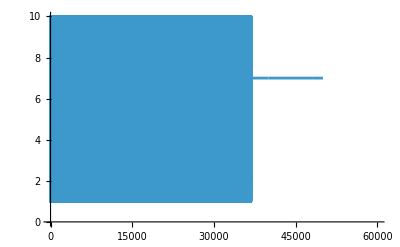

```mathematica
ListLinePlot[monQpricepath1,PlotRange->{{0,60000},{0,10}}]
```

```mathematica
(*The figure illustrates the sequence of prices chosen by Player 2 over time.Given that an equilibrium is defined as a set of price choices from which neither player deviates for a minimum of 100 episodes,the graph displays only those price selections observed up to the point at which this condition is satisfied. In that specific case never, thats why we see observations up until episode 50000*)
```

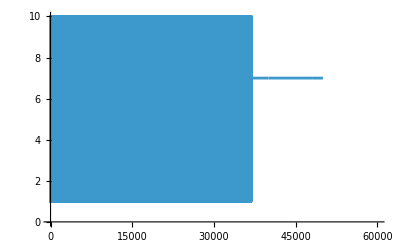

```mathematica
ListLinePlot[monQpricepath2,PlotRange->{{0,60000},{0,10}}]
```

```mathematica
(*The price combination of both players at time (t-1) is represented by the first two entries (e.g.,(7,7)),while the third (final) component denotes the price chosen by Player 1 at time (t) in response to these preceding prices.*)
```

```mathematica
monQpath1
```

```mathematica
(*The price combination of both players at time (t-1) is represented by the first two entries (e.g.,(7,7)),while the third (final) component denotes the price chosen by Player 2 at time (t) in response to these preceding prices.*)
```

```mathematica
monQpath2
```

```mathematica
(*chosen prices over time by player 1*)
```

```mathematica
monQpricepath1
```

```mathematica
(*chosen prices over time by player 2*)
```

```mathematica
monQpricepath2
```

```mathematica
(*Indicates the number of realized episodes required for an equilibrium to be reached.*)(*no equilibria was acchieved*)
```

```mathematica
distribution
```

{50002,50002}